```mathematica
(* Check Random*)
p=4;pp=2;q=2;r=2;
PermA=Permutations[Range[p+q+r]];
PermB=Permutations[Range[pp+q+r]];
PA=(p+q+r)!;
PB=(pp+q+r)!;
TrialN=2;
For[ind=1,ind≤TrialN, ind++,
i=RandomInteger[{1,PA}];
j=RandomInteger[{1,PB}];
xsol=VerifyConjectureSC1[p,pp,q,r,PermA[[i]],PermB[[j]]];
Print["A soution = ",xsol//MatrixForm];
If[ Length[xsol]≥(p+q+r)(p+q+r-1)/2,
(* Print["Solutions = ", xsol//MatrixForm]; *)
xsolna=Transpose[xsol][[1]];
xsolnb=Transpose[xsol][[3]];
sa=0;
sb=0;
For[k=1,k≤ Length[xsolna], k++,
sa+=Length[xsolna[[k]]];
sb+=Length[xsolnb[[k]]];
];
Print["sigma, tau = ",PermA[[i]],PermB[[j]],", Length = ",Length[xsol],", Number of a- & b-pairs used = ", sa/2, " & ", sb/2];
];
];
```

LinearProgramming::lpip: Warning: integer linear programming will use a machine precision approximation of the inputs.

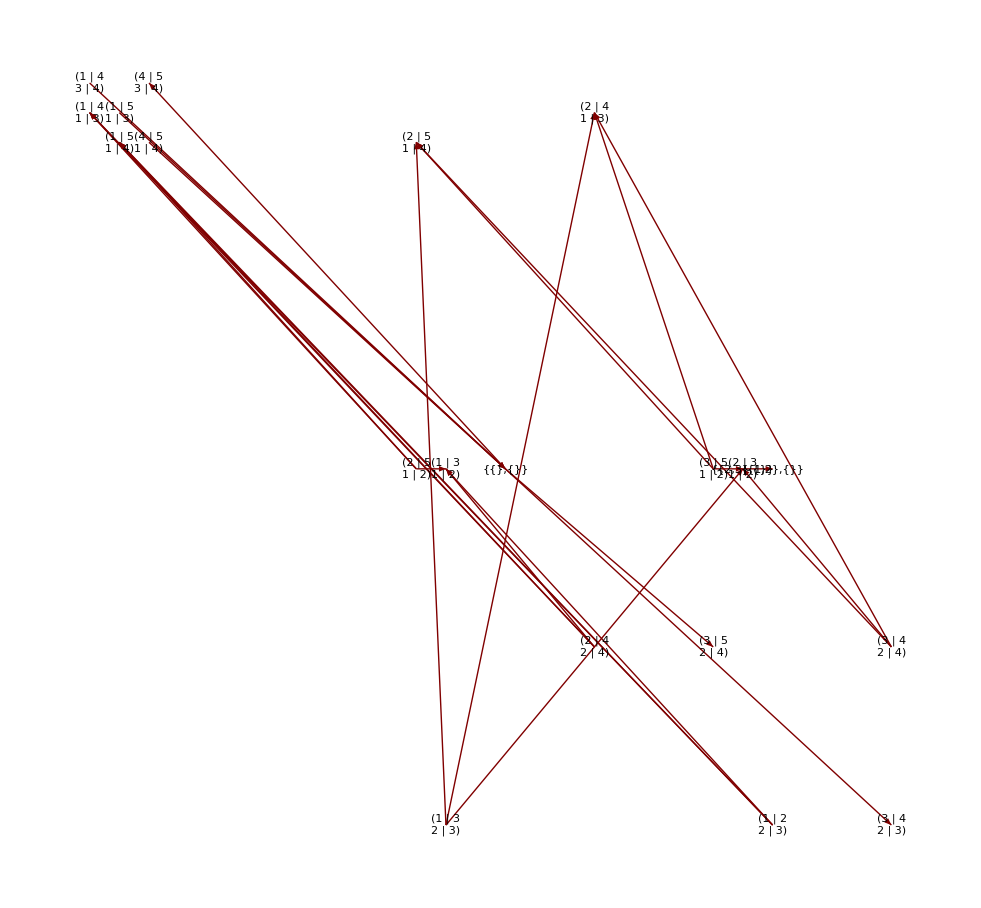
Plot of Farkas Set-Graphics-

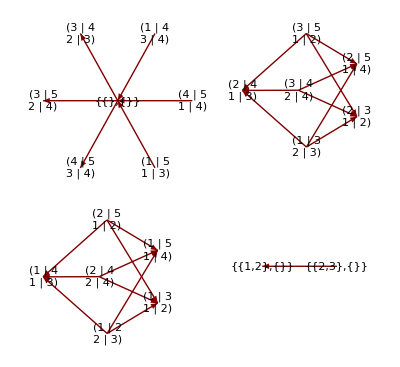
Some Graph Plot-Graphics-

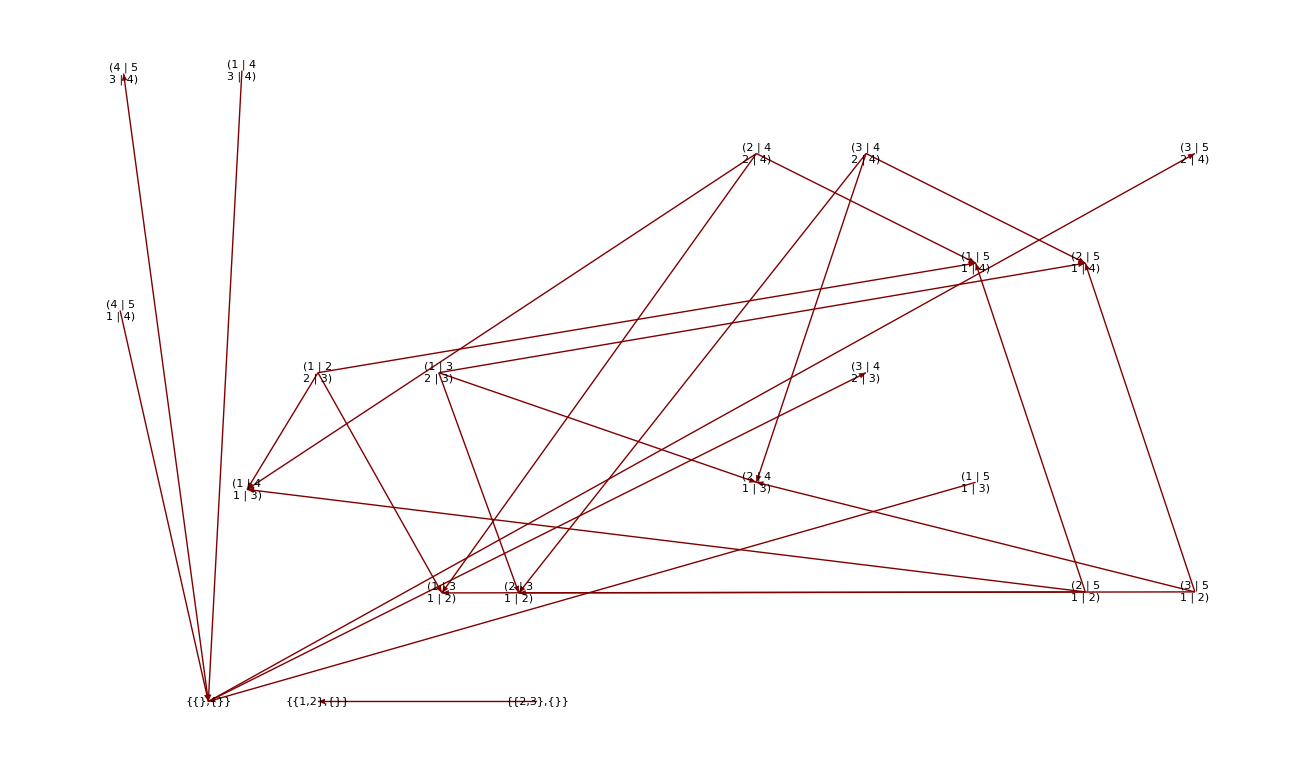
Some Graph Embedding in R^2-Graphics-

{9,-2,8,-14,3,13,-13,-3,7,-12,0,12,-12,11,-6,13}

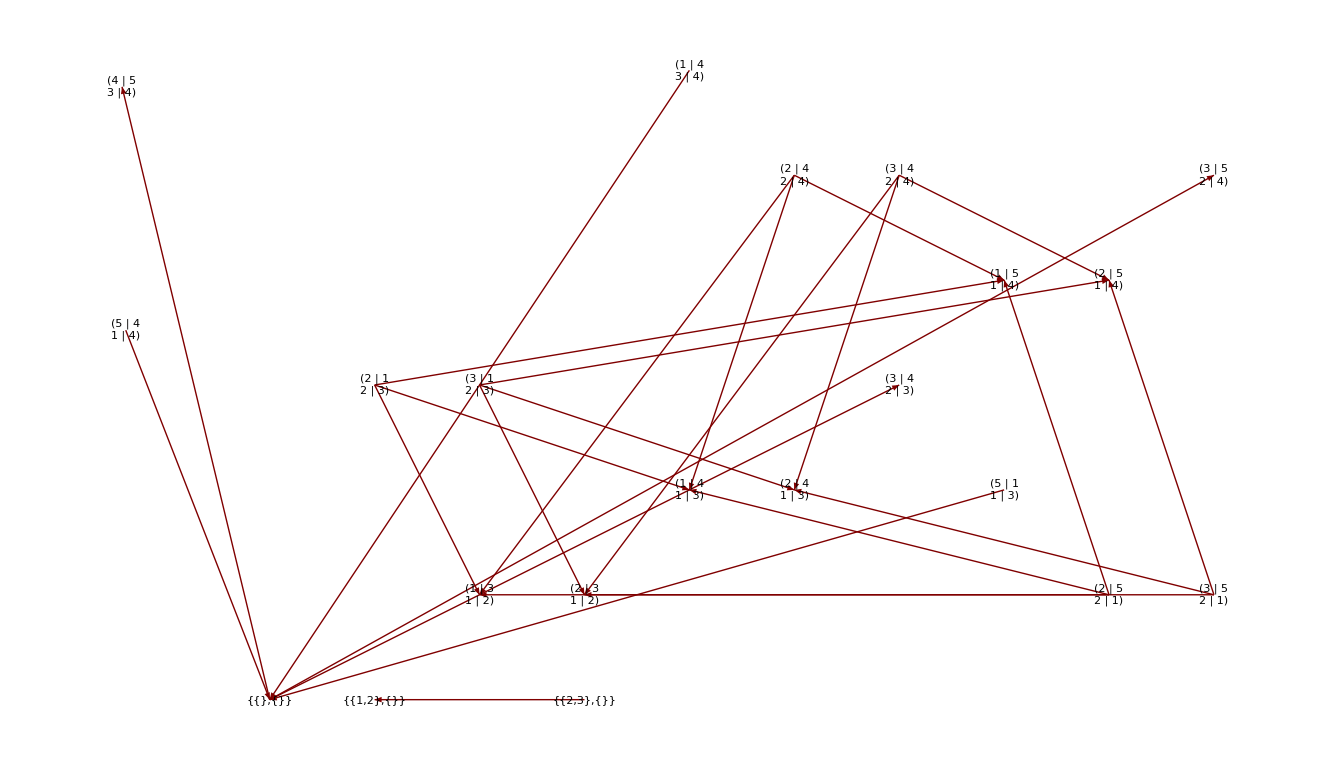
Some Graph Embedding in R^2-Graphics-

{9,-2,8,-14,3,13,-13,-3,7,-12,0,12,-12,11,-6,13}

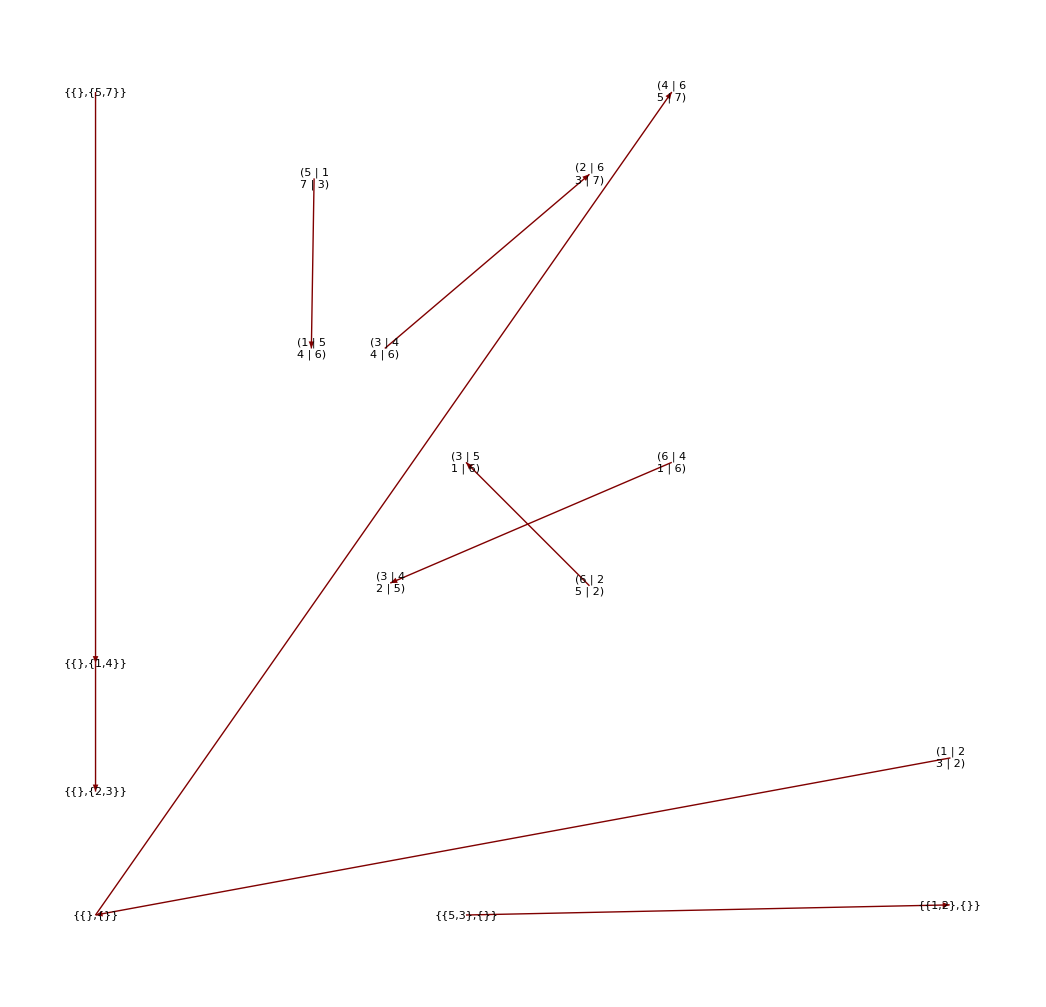
Tiling Graph-Graphics-

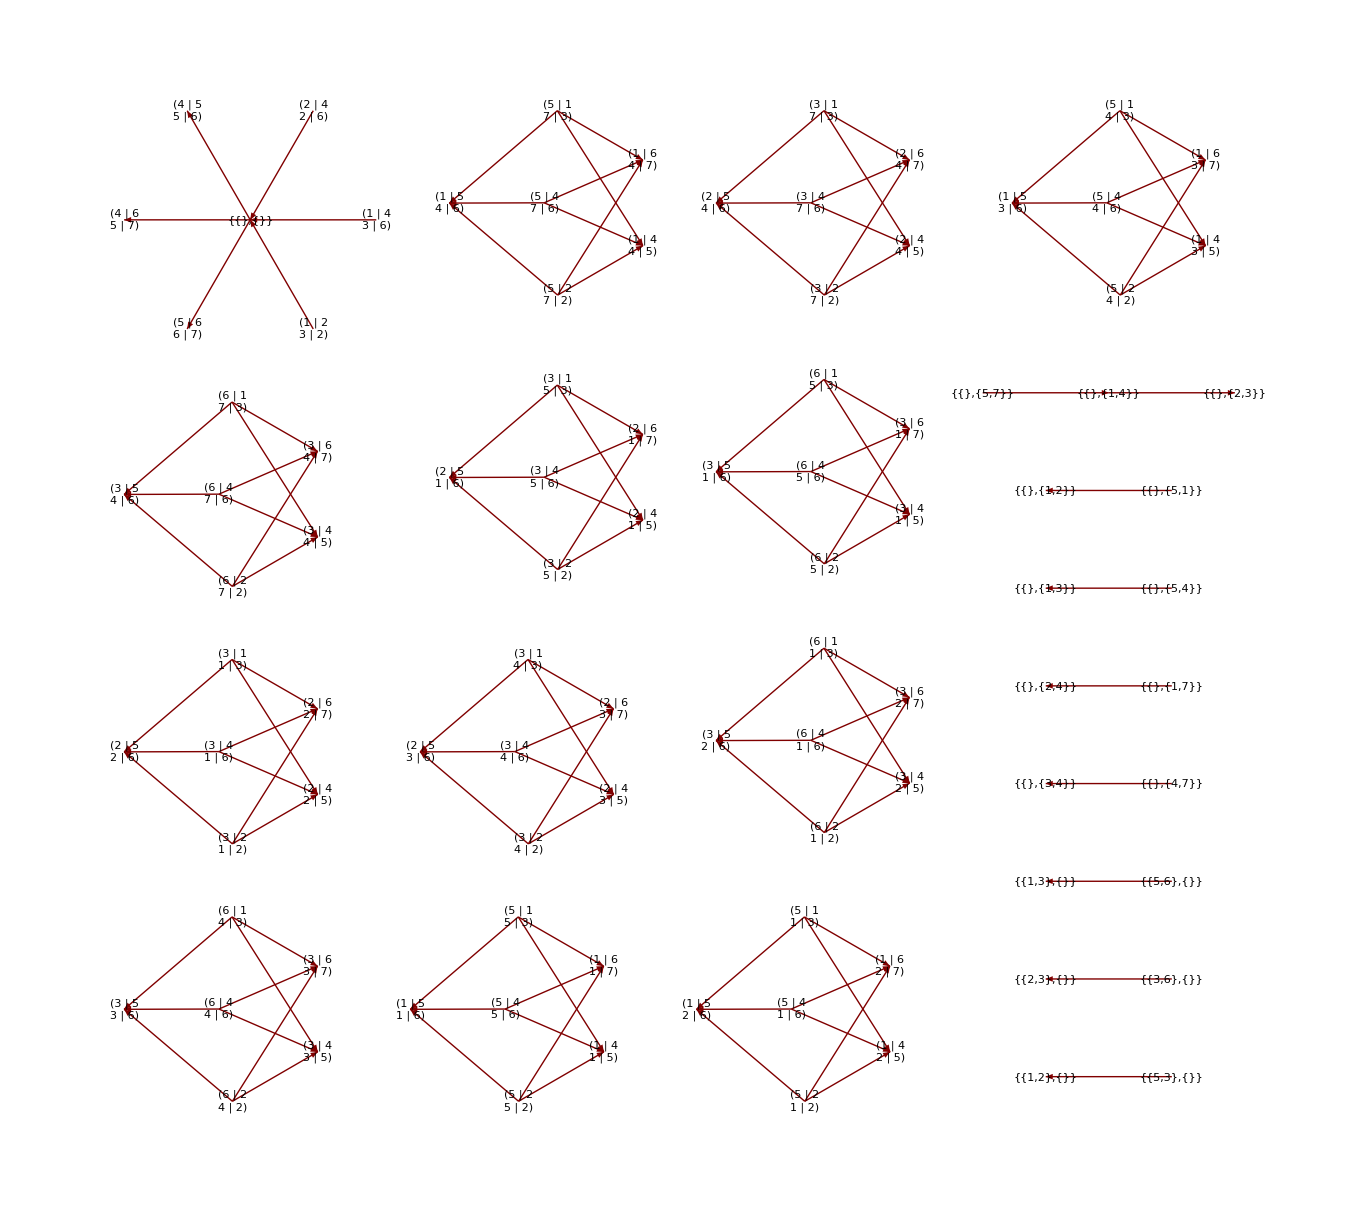
Some Graph Plot-Graphics-

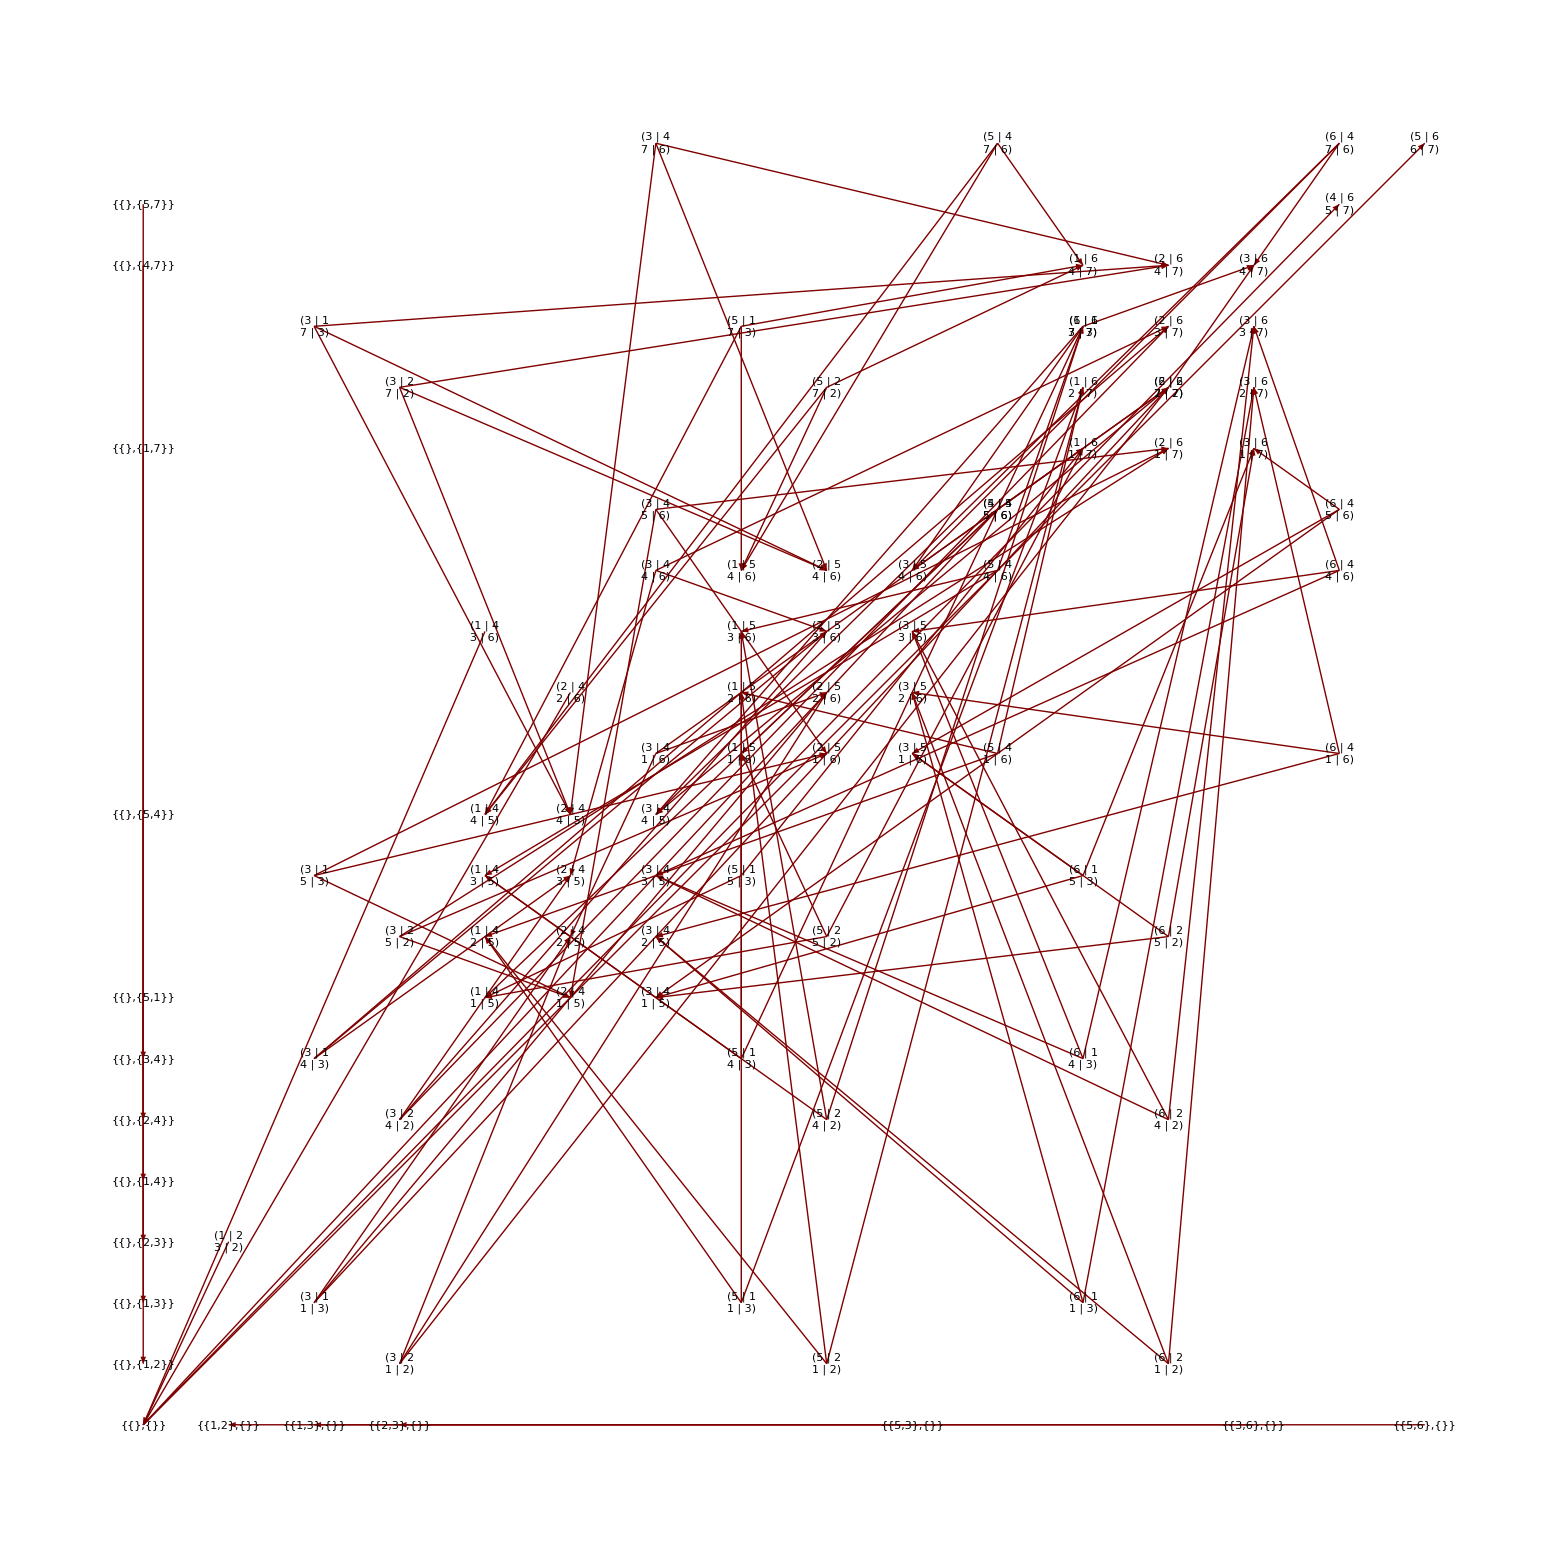
Some Graph Embedding in R^2-Graphics-

{{{1,2},{5,3},{},{}},{{},{},{1,4},{5,7}},{{},{},{2,3},{1,4}},{{4,6},{},{5,7},{}},{{},{1,2},{},{3,2}},{{1,5},{5,1},{4,6},{7,3}},{{2,6},{3,4},{3,7},{4,6}},{{3,4},{6,4},{2,5},{1,6}},{{3,5},{6,2},{1,6},{5,2}}}

```mathematica
{p,pp,q,r,sigma,tau}={2,1,0,3,{2,3,5,1,4},{2,1,3,4}};SCGraphPlot1[p,pp,q,r,sigma,tau]
```